# Chapter 4

## Setup

```mathematica
Unprotect[DivisorSigma];

DivisorSigma[m_Integer]:=DivisorSigma[1,m];
SyntaxInformation[DivisorSigma]={"ArgumentsPattern"->{_,_.}};
Format[HoldPattern[DivisorSigma[m_]],TraditionalForm]:=
σ[m];

Protect[DivisorSigma];
```

```mathematica
Attributes[DivisorTau]=Listable;

DivisorTau[n_Integer]:=
DivisorSigma[0,n];

Format[DivisorTau,TraditionalForm]=τ;
```

```mathematica
PerfectNumberQ[n_]:=
DivisorSigma[n]===2*n;
```

```mathematica
ClearAll[MersenneExponent];
MersenneExponent[1]=2;
MersenneExponent[n_Integer?Positive]:=MersenneExponent[n]=
Module[{p=NextPrime[MersenneExponent[n-1]]},
While[!PrimeQ[2^p-1],
p=NextPrime[p]];
p];

ClearAll[MersennePrime];
MersennePrime[n_Integer?Positive]:=MersennePrime[n]=2^MersenneExponent[n]-1;

Attributes[MersennePrime]=Listable;
```

```mathematica
PrimesTo[x_?Positive]:=Prime@Range@PrimePi@x;
PrimesTo[x_?NumericQ]/;Im[x]==0={};
```

## Introduction

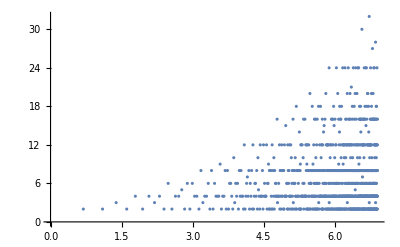

```mathematica
ListPlot[Table[{Log[n],DivisorTau[n]},{n,2,1000}],AxesOrigin->{0,0}]
```

```mathematica
Limit[(HarmonicNumber[n]-Log[n])/EulerGamma,n->Infinity]
```

1

### Exercise 4.0.3

```mathematica
data=Table[{n,Log[n!]/Log[n]},{n,2,50}];
```

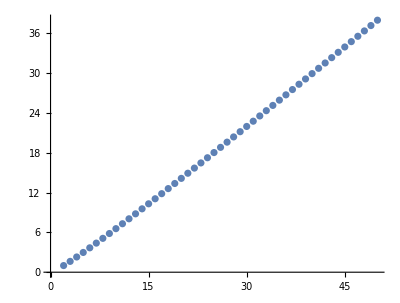

```mathematica
ListPlot[data,AspectRatio->Automatic]
```

```mathematica
fit=LinearModelFit[data,n,n]
```

FittedModel[-1.19254+0.776642 n]

```mathematica
Exp[fit["Function"][10]]
```

716.144

## Section 4.1

### Exercise 4.1.1

```mathematica
DivisorTau[8]
```

4

```mathematica
divisorLatticePlot[k_Integer?Positive]:=
With[{lattice=GroupBy[Tuples[Range[k+1],2],Times@@#==k&]},
ContourPlot[x*y==k,{x,0,10},{y,0,10},Epilog->{
Point@lattice@True
},
GridLines->Automatic
]]
```

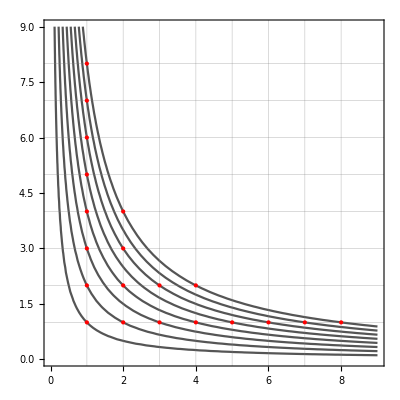

```mathematica
ContourPlot[
Table[x*y==k,{k,1,8}]//Evaluate,
{x,0,9},{y,0,9},
ContourStyle->Darker[Gray],
GridLines->{Range[1,8],Range[1,8]},

Epilog->
{Red,PointSize[Large],Point[Select[Tuples[Range[9],2],Times@@#≤8&]]}
]
```

```mathematica
Count[Tuples[Range[1,8],2],{x_,y_}/;x*y≤8]
```

20

### Exercise 4.1.2

```mathematica
{#,Total@#}&@DivisorTau[Range[8]]
```

{{1,2,2,3,2,4,2,4},20}

### Exercise 4.1.3

∑_(k=1)^n τ(k) is the number of points {x,y} ∈ℤ and x y ≤ n.

### Exercise 4.1.4

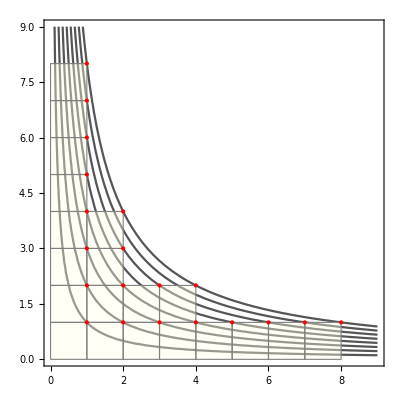

```mathematica
With[{points=Select[Tuples[Range[9],2],Times@@#≤8&]},
ContourPlot[
Table[x*y==k,{k,1,8}]//Evaluate,
{x,0,9},{y,0,9},
ContourStyle->Darker[Gray],
Epilog->
{EdgeForm@Directive[Thin,Gray],

FaceForm@Directive[Lighter@LightYellow,Opacity[0.4]],
Rectangle/@(points-1),
Red,PointSize[Large],Point[points]
}
]]
```

### Exercise 4.1.5

```mathematica
Integrate[n/x,{x,1,n},Assumptions->1≤n]
```

n Log[n]

### Exericse 4.1.6

The average order of τ(n) is log(n).

### Plot

```mathematica
Exp[7]//N
```

1096.63

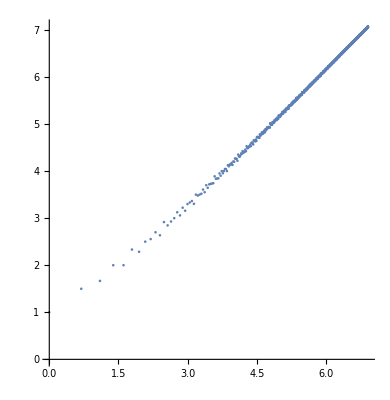

```mathematica
With[{ns=Range[1000]},
With[{taus=DivisorTau[ns]},
ListPlot[Transpose[{Log[#],Accumulate[taus]/#}&@ns],
AspectRatio->Automatic]]]
```

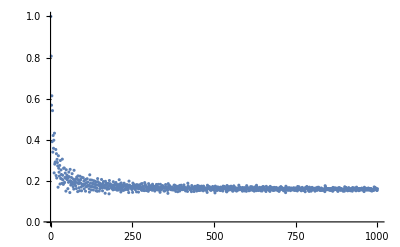

```mathematica
With[{ns=Range[1000]},
With[{taus=DivisorTau[ns]},
ListPlot[Accumulate[taus]/#-Log[#]&@ns,PlotRange->All]]]
```

### Exercise 4.2.1

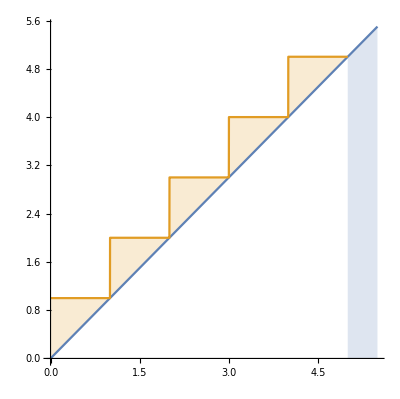

```mathematica
Show[
Plot[x,{x,5,5.5},
Filling->Axis,

AxesOrigin->{0,0}
],
Plot[{x,Ceiling[x]},{x,0,5},

Exclusions->None,

Filling->{2->{1}}],

AspectRatio->Automatic]
```

### Exercise 4.2.2

1/2 Floor[t] (Floor[t]+1)==1/2 (t+O(1)) (t+1+O(1))==1/2 t^2+2t O(1)+O(1)+1==t^2/2+O(t)

### Exercise 4.2.3

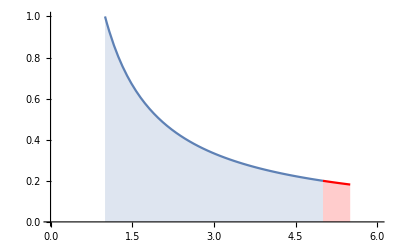

```mathematica
Show[
Plot[
1/t,{t,1,5},
AxesOrigin->{0,0},
Filling->Axis
],
Plot[
1/t,{t,5,5.5},
PlotStyle->Red,
AxesOrigin->{0,0},
Filling->Axis],


PlotRange->{{0,6},All}]
```

```mathematica
With[{ns=Range[1000]},
With[{taus=DivisorTau[ns]},
ListPlot[Accumulate[taus]/#-Log[#]&@ns,PlotRange->All,
GridLines->{None,{2*EulerGamma-1}},
GridLinesStyle->Directive[Black,Thick]
]]]
```

-Graphics-

### Exercise 4.2.4

```mathematica
approximateTauSum[n_]:=n*Log[n]+2(EulerGamma-1)*n
```

```mathematica
N@{1/3,27/82,15/46,12/37}
```

{0.333333,0.329268,0.326087,0.324324}

## Section 4.3

### Exercise 4.3.1

```mathematica
Accumulate[1/Range[3]^2]
```

{1,5/4,49/36}

```mathematica
?HarmonicNumber
```

HarmonicNumber[n] gives the n^th harmonic number H_n. 
HarmonicNumber[n,r] gives the harmonic number H_n^(r) of order r.

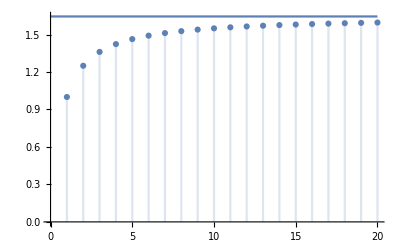

```mathematica
Show[
Plot[{Zeta[2]},{x,0,20},
PlotRange->All],
DiscretePlot[HarmonicNumber[n,2],{n,1,20},
Filling->Axis,AxesOrigin->{0,0}
]
]
```

### Proof

```mathematica
Integrate[x^(-2),{x,1,Infinity}]
```

1

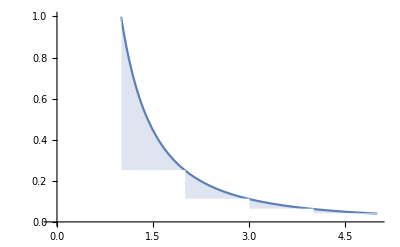

```mathematica
Show[
Plot[{1/x^2,1/Ceiling[x]^2},{x,1,5},AxesOrigin->{0,0},PlotRange->All,
PlotStyle->{Automatic,Transparent},
Filling->{1->{2}}
],
RectangleChart[Thread@{1,1/Range[5]^2},BarSpacing->None,ChartStyle->Directive[White,EdgeForm[Thickness[0.002]]]]]
```

### Exercise 4.3.2

```mathematica
tabulated=With[{n:=10^#},
With[{exprs={HarmonicNumber[n,2],Zeta[2]-1/n}},
Prepend[N[exprs,20],HoldForm[n]]]]&/@Range[0,6]
```

{{10^0,1.,0.64493406684822643647},{10^1,1.5497677311665406904,1.5449340668482264365},{10^2,1.6349839001848928651,1.6349340668482264365},{10^3,1.6439345666815598031,1.6439340668482264365},{10^4,1.6448340718480597698,1.6448340668482264365},{10^5,1.6449240668982262698,1.6449240668482264365},{10^6,1.6449330668487264363,1.6449330668482264365}}

```mathematica
Abs@*Subtract@@@tabulated[[All,{2,3}]]*ReleaseHold[tabulated[[All,1]]]^2
```

{0.3550659331517735635,0.48336643183142539,0.498333366664286,0.4998333333667,0.49998333333,0.499998333,0.4999998}

### Exercise 4.3.3 and 4.3.4

n3==∑_(k=1)^n 1/k^3

```mathematica
Integrate[1/x^3,{x,n,Infinity},Assumptions->0<n]
```

1/(2 n^2)

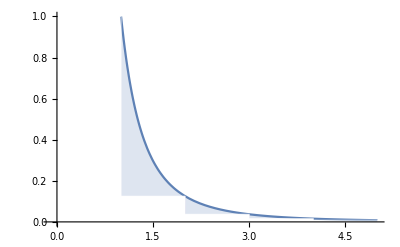

```mathematica
Show[
Plot[{1/x^3,1/Ceiling[x]^3},{x,1,5},AxesOrigin->{0,0},PlotRange->All,
PlotStyle->{Automatic,Transparent},
Filling->{1->{2}}
],
RectangleChart[Thread@{1,1/Range[5]^3},BarSpacing->None,ChartStyle->Directive[White,EdgeForm[Thickness[0.002]]]]]
```

3-n3==1/(2 n^2)+O(1/n^3)

```mathematica
N[Zeta[3]-HarmonicNumber[#,3]-1/(2*#^2),20]*#^3&/@(10^Range[4])
```

{-0.47508251459896626895,-0.49750008332500149958,-0.49975000008333325,-0.49997500000008333333}

## Section 4.4

### Exercise 4.4.1

∑_(n=1)^k σ(k)==(n^2 2)/2+O(n log(n))

Abs[∑_(k=1)^n σ(k)-(n^2 2)/2]≤C n log(n)

### Exercise 4.4.2

Trivial.

### Exercise 4.4.3